```mathematica
Exit[]
```

```mathematica
A:={{1, 3},{6,4}}
```

```mathematica
MatrixForm [A]
```

(1 | 3
6 | 4)

```mathematica
({{1, 3}, {6, 4}})
```

{{1,3},{6,4}}

```mathematica
Inverse[A]
```

{{-2/7,3/14},{3/7,-1/14}}

```mathematica
MatrixForm[Inverse[A]]
```

(-2/7 | 3/14
3/7 | -1/14)

```mathematica
Eigensystem[A][[2]]
```

{{1,2},{-1,1}}

```mathematica
Eigensystem[A][[1]]
```

{7,-2}

```mathematica
Eigensystem[A]
```

{{7,-2},{{1,2},{-1,1}}}

```mathematica
Eigensystem[{A,-2}]
```

Eigensystem::matrix: Argument -2 at position 2 is not a non-empty rectangular matrix.

Eigensystem[{{{1,3},{6,4}},-2}]

```mathematica
f[x_]:=x^{1/3}
```

```mathematica
f'[x]
```

{1/(3 x^(2/3))}

```mathematica
D[f[x], x]
```

{1/(3 x^(2/3))}

```mathematica
D[f[x], x]/.x->0
```

Power::infy: Infinite expression 1/0^(2/3) encountered.

{ComplexInfinity}

```mathematica
Plot[f[x], {x, -4, 4}, PlotLabels->"Expressions"]
```

-Graphics-

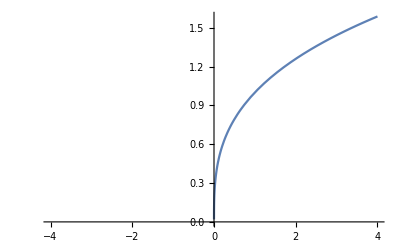

```mathematica
Plot[f[x], {x, -4, 4}, PlotLegends->"Expressions"]
```

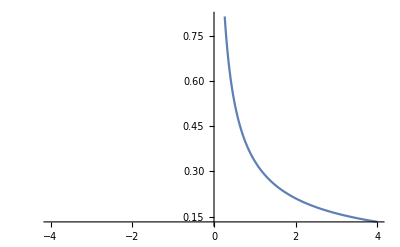

```mathematica
Plot[f'[x], {x, -4, 4}]
```

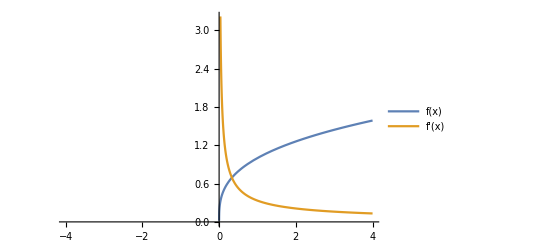

```mathematica
Plot[{f[x], f'[x]}, {x, -4, 4}, PlotLegends->"Expressions"]
```

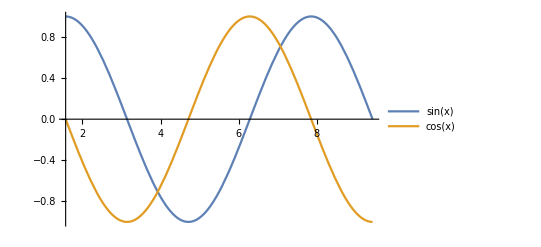

```mathematica
Plot[{Sin[x], Cos[x]}, {x, Pi/2, 3Pi}, PlotLegends->"Expressions"]
```

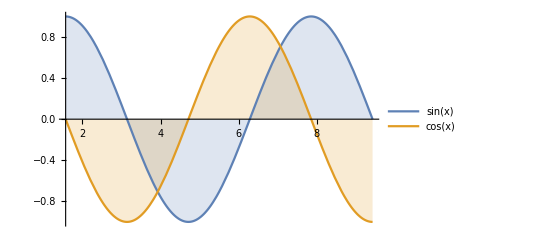

```mathematica
Plot[{Sin[x], Cos[x]}, {x, Pi/2, 3Pi}, PlotLegends->"Expressions", Filling->Axis]
```

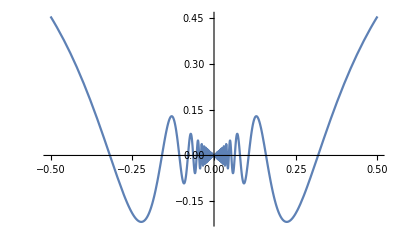

```mathematica
Plot[x Sin[1/x], {x, -1/2, 1/2}, PlotLegends->"Expressions"]
```

```mathematica
Lx=1;Ly=1;Lz=1;(*Dimensions of the box*)nx=1;ny=1;nz=1;(*Quantum numbers*)(*Wavefunction definition*)wavefunction[x_,y_,z_]:=Sqrt[8/(Lx Ly Lz)] Sin[nx Pi x/Lx] Sin[ny Pi y/Ly] Sin[nz Pi z/Lz];

(*Plot the wavefunction in 3D*)
Plot3D[Evaluate[wavefunction[x,y,Lz/2]],(*Slice at z=Lz/2*){x,0,Lx},{y,0,Ly},PlotRange->All,AxesLabel->{"x","y","ψ(x, y, z)"},PlotLabel->"Wavefunction at z = Lz/2",ColorFunction->"Rainbow",Mesh->None]
```

-Graphics3D-

```mathematica
h[t_]:=Piecewise[{{Exp[-t], t>0}}, 0]
```

```mathematica
h[1]
```

1/ⅇ

```mathematica
h[-1]
```

0

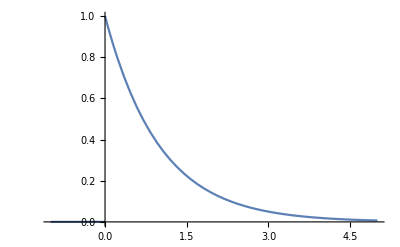

```mathematica
Plot[h[t], {t, -1,5}, PlotRange->All]
```

```mathematica
F[ω_]:=FourierTransform[h[t],t,ω]
F[ω]
```

ⅈ/(√(2 π) (ⅈ+ω))

```mathematica
G[ω_]:=FourierTransform[h[t] UnitStep[t],t,ω]
G[ω]
```

ⅈ/(√(2 π) (ⅈ+ω))

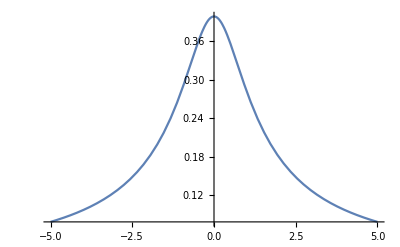

```mathematica
Plot[Abs[F[ω]], {ω, -5, 5}]
```

```mathematica
Plot[F[ω], {ω, -5, 5}]
```

-Graphics-

```mathematica
g[t_]:=InverseFourierTransform[G[ω], ω, t]
g[t]
```

ⅇ^-t HeavisideTheta[t]

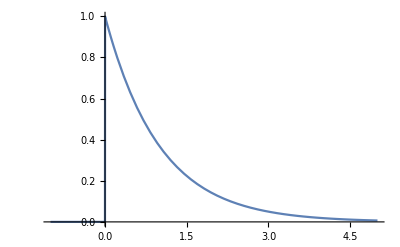

```mathematica
Plot[g[t], {t, -1, 5}]
```

```mathematica
f[t_]:=Sin[t]+Sin[3t]+Sin[5t];
f[t]
```

Sin[t]+Sin[3 t]+Sin[5 t]

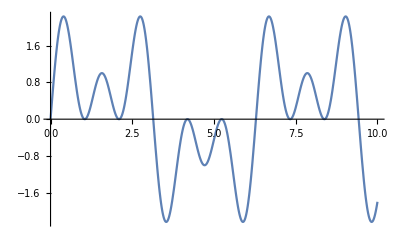

```mathematica
Plot[f[t], {t, 0, 10}]
```

```mathematica
F[ω_]:=FourierTransform[f[t], t, ω];
F[ω];
```

```mathematica
Abs[(List @@ F[ω])[[1]]]
```

√(π/2) Abs[DiracDelta[-5+ω]]

```mathematica
F[ω][[1]]
```

ⅈ √(π/2) DiracDelta[-5+ω]

```mathematica
NIntegrate[(List @@ F[ω])[[1]], {ω,1,5}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
Plot[Abs[(List @@ F[ω])[[1]]], {ω, -1, 1}, PlotRange->{{-1, 1}, {0, 2}}, PlotStyle->{Red}, ExclusionsStyle->Directive[Thick,Blue]]
```

-Graphics-

```mathematica
f[t_]:=ⅈ Sin[t]+ Cos[t];
f[t]
F[ω]:=FourierTransform[f[t], t,ω];
F[ω]
```

Cos[t]+ⅈ Sin[t]

√(2 π) DiracDelta[1+ω]

```mathematica
Integrate[F[ω], {ω, -∞, +∞}]
```

√(2 π)

```mathematica
Plot[Integrate[F[ω], {ω, -∞, +∞}],{ω,-1,1},  PlotRange->{{-5, 5}, {0, 2}}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-∞,∞}.

NIntegrate::itraw: Raw object -0.999959 cannot be used as an iterator.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at t = ∞.

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

NIntegrate::itraw: Raw object -0.999959 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.959143,-∞,∞}.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.918326,-∞,∞}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

```mathematica
f[t_]:=Sin[t];
f[t]
F[ω]:=FourierTransform[f[t], t,ω];
F[ω]
```

Sin[t]

ⅈ √(π/2) DiracDelta[-1+ω]-ⅈ √(π/2) DiracDelta[1+ω]

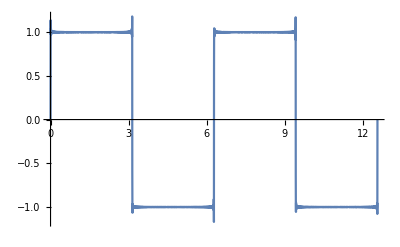

```mathematica
f=0;
Do[f+={4/Pi}{1/n}Sin[n t],{n, 1, 1000, 2}];
f;
Plot[f,{t, 0, 4 Pi}]
```

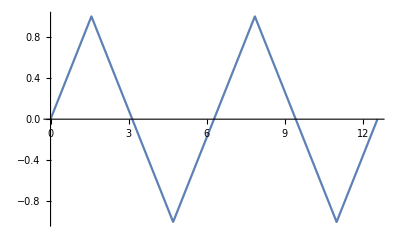

```mathematica
f=0;
Do[f+={8/Pi^2}{{-1}^{{n-1}/2}/n^2}Sin[n t],{n, 1, 1000, 2}];
f;
Plot[f,{t, 0, 4 Pi}]
```

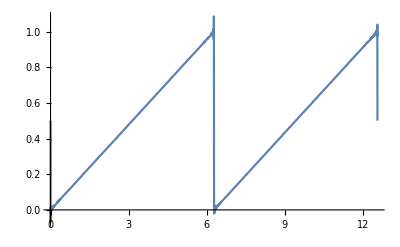

```mathematica
f=1/2;
Do[f-={1/Pi}{1/n }Sin[n t],{n, 1, 1000, 1}];
f;
Plot[f,{t, 0, 4 Pi}]
```